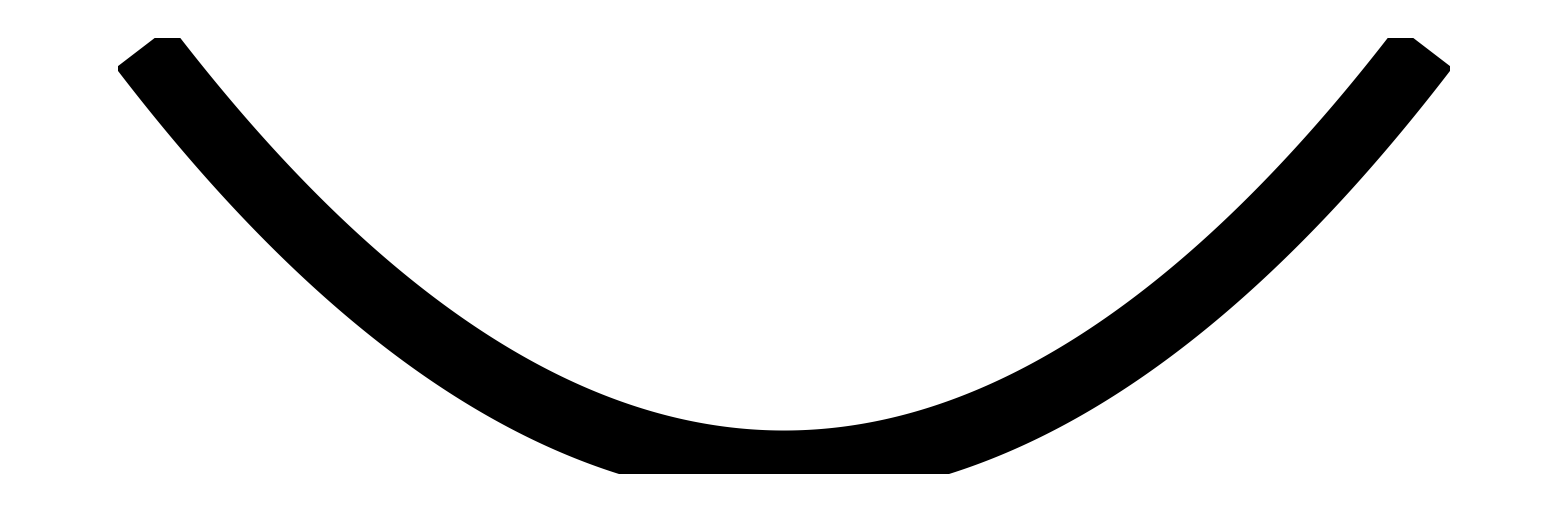

```mathematica
l1=Table[{x,0.02x^2},{x,-10,10,0.01}];
g=Graphics[{Thickness[0.05],Line[l1]},ImageSize->{2048,512},Background->None]
```

```mathematica
Export["parabolla.png",Image[g]]
```

parabolla.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["parabolla.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["parabolla.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["parabolla.png"]]]
```

```mathematica
tb=Table[Print[t];,{t,0,1,0.02}];
```

$Aborted

```mathematica
n=500;
For[i=1,i≤n,i++,Export["/Users/eliottmorgensztern/Documents/Mathematica/Images/Lenses/"<>ToString[i]<>".png",
getImage[i/n],Background->None,ImageSize->{2048*2,2048}]]
```

$Aborted

```mathematica
Export["/Users/eliottmorgensztern/Documents/Mathematica/Images/Lenses/1.png",tb[[300]],Background->None]
```

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

$Failed

```mathematica
Manipulate[Rasterize[Region[DiscretizeRegion[RegionIntersection[Disk[{0,0},1000],Disk[{1.8*t*1000,0},1000]],PrecisionGoal->5,ImageSize->{1000,1000}],ImageSize->{4096,2048}],Background->None],{t,0,1}]
```

```mathematica
getImage[i_]:=(im=Rasterize[Region[DiscretizeRegion[RegionIntersection[Disk[{0,0},1000],Disk[{1.95*i*1000,0},1000]],PrecisionGoal->5,ImageSize->{1000,1000}]],Background->None];
Return[
Graphics[{RGBColor[{0,0,0,0}],Rectangle[{0,0},{4096,2048}],Inset[im,{4096/3,1024}, Automatic,2130]},PlotRange->{{0,4096},{0,2048}},Background->None]
])
getImage[0]
```

-Graphics-

```mathematica
Export["/Users/eliottmorgensztern/Documents/Mathematica/Images/Lenses/1.png"
,im,ImageSize->{2048*2,2048}]
```

/Users/eliottmorgensztern/Documents/Mathematica/Images/Lenses/1.png

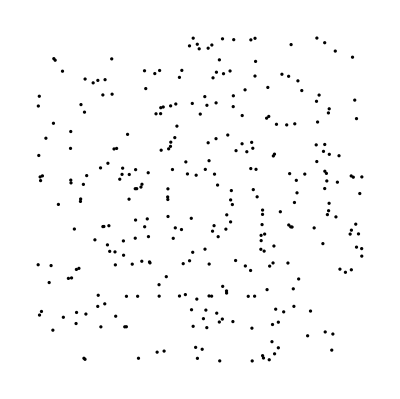

```mathematica
g=Graphics[Flatten[Table[Table[Disk[{r Cos[θ-RandomReal[{-0.5,0.5}]],r Sin[θ-RandomReal[{-0.5,0.5}]]},0.05],{θ,0,2 Pi,Pi/(10r)}],{r,1,5,1}]],ImageMargins->100]
```

```mathematica
Export["Documents/Wolfram Mathematica/disk cloud.png",g,Background->None,ImageSize->{2048,2048}]
```

Documents/Wolfram Mathematica/disk cloud.png